```mathematica
data =Import["/Users/bbn/Desktop/PhyExp/College-Physics-Experiment/Exp6/A1.xlsx"]
```

{{{硅光电池暗伏安特性曲线（正向）,},{电压U/V,电流I/mA},{0.6039,1.},{0.7135,2.},{0.7849,3.},{0.8335,4.},{0.8802,5.},{0.9134,6.},{0.9439,7.},{0.9724,8.},{0.99,9.},{1.0222,10.},{1.049,11.},{1.0694,12.},{1.0892,13.},{1.1096,14.},{1.1257,15.},{1.1462,16.},{1.1619,17.},{1.1787,18.},{1.1962,19.},{1.2118,20.}}}

```mathematica
data1 = data[[1]][[3;;]]
```

{{0.6039,1.},{0.7135,2.},{0.7849,3.},{0.8335,4.},{0.8802,5.},{0.9134,6.},{0.9439,7.},{0.9724,8.},{0.99,9.},{1.0222,10.},{1.049,11.},{1.0694,12.},{1.0892,13.},{1.1096,14.},{1.1257,15.},{1.1462,16.},{1.1619,17.},{1.1787,18.},{1.1962,19.},{1.2118,20.}}

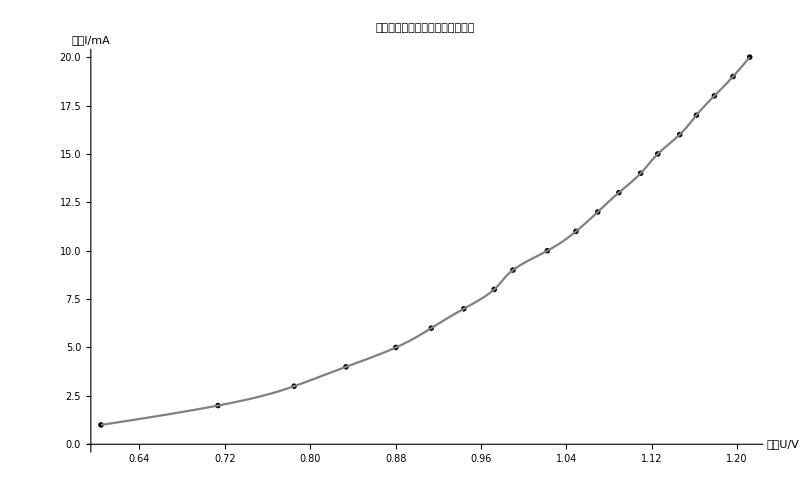

```mathematica
Show[
ListPlot[data1,PlotStyle->Black,PlotMarkers->{Style["X",10]}],
ListLinePlot[data1,PlotStyle->Gray, InterpolationOrder->4],
AxesLabel->{Style[data[[1]][[2]][[1]],15,Bold],Style[data[[1]][[2]][[2]],15,Bold]},
AxesStyle->Directive[Arrowheads[0.03],13],
PlotLabel->Style[data[[1]][[1]][[1]],18,FontFamily->"Adobe Fan Heiti Std",Bold],
ImageSize->{800,500}]
```

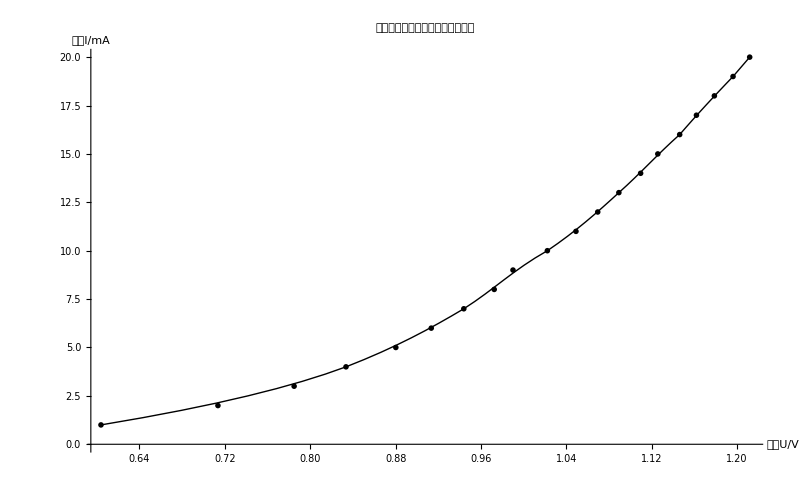

```mathematica
Show[
ListPlot[data1,PlotStyle->Black,PlotMarkers->{Style["X",10]}],
Graphics[BezierCurve[data1,SplineDegree->3]],
AxesLabel->{Style[data[[1]][[2]][[1]],15,Bold],Style[data[[1]][[2]][[2]],15,Bold]},
AxesStyle->Directive[Arrowheads[0.03],20],
PlotLabel->Style[data[[1]][[1]][[1]],18,FontFamily->"Adobe Fan Heiti Std",Bold],
ImageSize->{800,500}]
```